```mathematica
proj[v_]:=Orthogonalize[{{1,-1,0,0},{0,1,-1,0},{0,0,1,-1}}].v
```

```mathematica
proj[{1,-1,0,0}]
```

{√2,0,0}

```mathematica
N@proj[{3/4,-1/4,-1/4,-1/4}]
```

{0.707107,0.408248,0.288675}

```mathematica
N@proj[{-1/4,3/4,-1/4,-1/4}]
```

{-0.707107,0.408248,0.288675}

```mathematica
N@proj[{-1/4,-1/4,3/4,-1/4}]
```

{0.,-0.816497,0.288675}

```mathematica
N@proj[{-1/4,-1/4,-1/4,3/4}]
```

{0.,0.,-0.866025}

```mathematica
vertices={{1,-1,0,0},{1,0,-1,0},{1,0,0,-1},{0,1,-1,0},{0,1,0,-1},{0,0,1,-1}}
vertices=Join[vertices,-vertices]
```

{{1,-1,0,0},{1,0,-1,0},{1,0,0,-1},{0,1,-1,0},{0,1,0,-1},{0,0,1,-1}}

{{1,-1,0,0},{1,0,-1,0},{1,0,0,-1},{0,1,-1,0},{0,1,0,-1},{0,0,1,-1},{-1,1,0,0},{-1,0,1,0},{-1,0,0,1},{0,-1,1,0},{0,-1,0,1},{0,0,-1,1}}

```mathematica
pvertices=proj/@vertices
```

{{√2,0,0},{1/(√2),√(2/3)+1/(√6),0},{1/(√2),1/(√6),1/(2 √3)+(√3)/2},{-1/(√2),√(2/3)+1/(√6),0},{-1/(√2),1/(√6),1/(2 √3)+(√3)/2},{0,-√(2/3),1/(2 √3)+(√3)/2},{-√2,0,0},{-1/(√2),-√(2/3)-1/(√6),0},{-1/(√2),-1/(√6),-1/(2 √3)-(√3)/2},{1/(√2),-√(2/3)-1/(√6),0},{1/(√2),-1/(√6),-1/(2 √3)-(√3)/2},{0,√(2/3),-1/(2 √3)-(√3)/2}}

```mathematica
ListPointPlot3D[proj/@vertices//Simplify,PlotRange->{{-2,2},{-2,2},{-2,2}},BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
vertices.vertices[[6]]
```

{0,-1,1,-1,1,2,0,1,-1,1,-1,-2}

```mathematica
{{0,0,0}}
```

{{0,0,0}}

Thread::tdlen: Objects of unequal length in {{1,-1,0,0},{1,0,-1,0},{1,0,0,-1},{0,1,-1,0},{0,1,0,-1},{0,0,1,-1},{-1,1,0,0},{-1,0,1,0},{-1,0,0,1},{0,-1,1,0},{0,-1,0,1},{0,0,-1,1}}+{0,0,0} cannot be combined.

{0,0,0}+{{1,-1,0,0},{1,0,-1,0},{1,0,0,-1},{0,1,-1,0},{0,1,0,-1},{0,0,1,-1},{-1,1,0,0},{-1,0,1,0},{-1,0,0,1},{0,-1,1,0},{0,-1,0,1},{0,0,-1,1}}

```mathematica
Outer[Plus,vertices,{{0,0,0}}]
```

{{{{1,1,1}},{{-1,-1,-1}},{{0,0,0}},{{0,0,0}}},{{{1,1,1}},{{0,0,0}},{{-1,-1,-1}},{{0,0,0}}},{{{1,1,1}},{{0,0,0}},{{0,0,0}},{{-1,-1,-1}}},{{{0,0,0}},{{1,1,1}},{{-1,-1,-1}},{{0,0,0}}},{{{0,0,0}},{{1,1,1}},{{0,0,0}},{{-1,-1,-1}}},{{{0,0,0}},{{0,0,0}},{{1,1,1}},{{-1,-1,-1}}},{{{-1,-1,-1}},{{1,1,1}},{{0,0,0}},{{0,0,0}}},{{{-1,-1,-1}},{{0,0,0}},{{1,1,1}},{{0,0,0}}},{{{-1,-1,-1}},{{0,0,0}},{{0,0,0}},{{1,1,1}}},{{{0,0,0}},{{-1,-1,-1}},{{1,1,1}},{{0,0,0}}},{{{0,0,0}},{{-1,-1,-1}},{{0,0,0}},{{1,1,1}}},{{{0,0,0}},{{0,0,0}},{{-1,-1,-1}},{{1,1,1}}}}

```mathematica
Distribute[{{0,0,0}},vertices]
```

{{1,-1,0,0},{1,0,-1,0},{1,0,0,-1},{0,1,-1,0},{0,1,0,-1},{0,0,1,-1},{-1,1,0,0},{-1,0,1,0},{-1,0,0,1},{0,-1,1,0},{0,-1,0,1},{0,0,-1,1}}[{{0,0,0}}]

```mathematica
pvertices0=Join[{{0,0,0}},pvertices]
```

{{0,0,0},{√2,0,0},{1/(√2),√(2/3)+1/(√6),0},{1/(√2),1/(√6),1/(2 √3)+(√3)/2},{-1/(√2),√(2/3)+1/(√6),0},{-1/(√2),1/(√6),1/(2 √3)+(√3)/2},{0,-√(2/3),1/(2 √3)+(√3)/2},{-√2,0,0},{-1/(√2),-√(2/3)-1/(√6),0},{-1/(√2),-1/(√6),-1/(2 √3)-(√3)/2},{1/(√2),-√(2/3)-1/(√6),0},{1/(√2),-1/(√6),-1/(2 √3)-(√3)/2},{0,√(2/3),-1/(2 √3)-(√3)/2}}

```mathematica
includeTranslates[lst_]:=Union[(Plus@@#)&/@Tuples[{lst,pvertices0}]//FullSimplify]
```

```mathematica
Nest[includeTranslates,{{0,0,0}},1]^2//Simplify
```

{{0,0,0},{0,2/3,4/3},{0,2/3,4/3},{1/2,3/2,0},{1/2,3/2,0},{1/2,1/6,4/3},{1/2,1/6,4/3},{1/2,3/2,0},{1/2,3/2,0},{1/2,1/6,4/3},{1/2,1/6,4/3},{2,0,0},{2,0,0}}

```mathematica
ClearAll[includeTranslates2]
```

```mathematica
includeTranslates2[v_List/;EvenQ[v[[1]]]]:=(Plus@@#)&/@Tuples[{{v},qvertices0}]
includeTranslates2[v_List/;OddQ[v[[1]]]]:=(Plus@@#)&/@Tuples[{{v},-qvertices0}]
includeTranslates2List[lst_]:=Union[Flatten[includeTranslates2/@lst,1]]
```

```mathematica
Table[Length[Nest[includeTranslates2List,{{0,0,0,0}},n]],{n,0,10}]
```

{1,5,17,41,83,147,239,363,525,729,981}

```mathematica
Differences[%65]
```

{4,12,24,42,64,92,124,162,204,252}

```mathematica
Factor[(1+2*x+4*x^2+2*x^3+x^4)/((1-x)^3*(1+x))]
```

-(1+2 x+4 x^2+2 x^3+x^4)/((-1+x)^3 (1+x))

```mathematica
Series[%69,{x,0,20}]
```

1+4 x+12 x^2+24 x^3+42 x^4+64 x^5+92 x^6+124 x^7+162 x^8+204 x^9+252 x^10+304 x^11+362 x^12+424 x^13+492 x^14+564 x^15+642 x^16+724 x^17+812 x^18+904 x^19+1002 x^20+O[x]^21

```mathematica
Differences[%]
```

{8,12,18,22,28,32,38,42,48}

```mathematica
Differences[%]
```

{4,6,4,6,4,6,4,6}

```mathematica
Flatten[includeTranslates2/@{{0,0,0,0}},1]
```

{{-3,1,1,1},{1,-3,1,-1},{1,1,-3,1},{1,1,1,-3},{0,0,0,0}}

```mathematica
qvertices={{3,-1,-1,-1},{-1,3,-1,1},{-1,-1,3,-1},{-1,-1,-1,3}}
qvertices0=Join[qvertices,{{0,0,0,0}}]
```

{{3,-1,-1,-1},{-1,3,-1,1},{-1,-1,3,-1},{-1,-1,-1,3}}

{{3,-1,-1,-1},{-1,3,-1,1},{-1,-1,3,-1},{-1,-1,-1,3},{0,0,0,0}}

```mathematica
Table[KeySort@Counts[Norm/@Nest[includeTranslates,{{0,0,0}},n]^2//Simplify],{n,0,5}]
```

{<|0→1|>,<|0→1,2→12|>,<|0→1,2→12,4→6,6→24,8→12|>,<|0→1,2→12,4→6,6→24,8→12,10→24,12→8,14→48,18→12|>,<|0→1,2→12,4→6,6→24,8→12,10→24,12→8,14→48,16→6,18→36,20→24,22→24,24→24,26→48,32→12|>,<|0→1,2→12,4→6,6→24,8→12,10→24,12→8,14→48,16→6,18→36,20→24,22→24,24→24,26→72,30→48,32→12,34→48,36→24,38→48,42→48,50→12|>}

```mathematica
Export["positions.json",N@Select[Nest[includeTranslates,{{0,0,0}},4]//Simplify,Norm[#]^2≤24&]]
```

positions.json

```mathematica
%62//MatrixForm
```

(<|0→1|>
<|0→1,2→12|>
<|0→1,2→12,4→6,6→24,8→12|>
<|0→1,2→12,4→6,6→24,8→12,10→24,12→8,14→48,18→12|>
<|0→1,2→12,4→6,6→24,8→12,10→24,12→8,14→48,16→6,18→36,20→24,22→24,24→24,26→48,32→12|>
<|0→1,2→12,4→6,6→24,8→12,10→24,12→8,14→48,16→6,18→36,20→24,22→24,24→24,26→72,30→48,32→12,34→48,36→24,38→48,42→48,50→12|>)

```mathematica
{1,12,6,
```

```mathematica
includeTranslates[{{0,0,0}}]
```

{{0,0,0},{0,-√(2/3),1/(2 √3)+(√3)/2},{0,√(2/3),-1/(2 √3)-(√3)/2},{-1/(√2),-1/(√6),-1/(2 √3)-(√3)/2},{-1/(√2),1/(√6),1/(2 √3)+(√3)/2},{-1/(√2),-√(2/3)-1/(√6),0},{-1/(√2),√(2/3)+1/(√6),0},{1/(√2),-1/(√6),-1/(2 √3)-(√3)/2},{1/(√2),1/(√6),1/(2 √3)+(√3)/2},{1/(√2),-√(2/3)-1/(√6),0},{1/(√2),√(2/3)+1/(√6),0},{-√2,0,0},{√2,0,0}}

```mathematica
Union[(Plus@@#)&/@Tuples[{{{0,0,0}},pvertices0}]]
```

{{0,0,0},{0,-√(2/3),1/(2 √3)+(√3)/2},{0,√(2/3),-1/(2 √3)-(√3)/2},{-1/(√2),-1/(√6),-1/(2 √3)-(√3)/2},{-1/(√2),1/(√6),1/(2 √3)+(√3)/2},{-1/(√2),-√(2/3)-1/(√6),0},{-1/(√2),√(2/3)+1/(√6),0},{1/(√2),-1/(√6),-1/(2 √3)-(√3)/2},{1/(√2),1/(√6),1/(2 √3)+(√3)/2},{1/(√2),-√(2/3)-1/(√6),0},{1/(√2),√(2/3)+1/(√6),0},{-√2,0,0},{√2,0,0}}

```mathematica
n(n+1)/2+n(n-1)/2//Simplify
```

n^2

```mathematica
(Sum[q^(n^2),{n,-5,5}]^3+Sum[(-q)^(n^2),{n,-5,5}]^3)/2//Expand
```

1+12 q^2+6 q^4+24 q^6+12 q^8+24 q^10+8 q^12+48 q^14+6 q^16+36 q^18+24 q^20+24 q^22+24 q^24+72 q^26+48 q^30+12 q^32+48 q^34+24 q^36+48 q^38+48 q^42+8 q^48+60 q^50+24 q^54+24 q^66

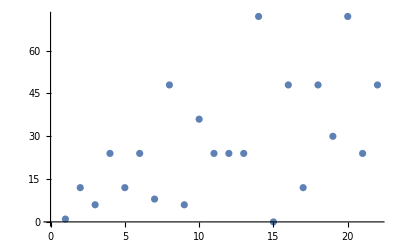

```mathematica
ListPlot[{1,12,6,24,12,24,8,48,6,36,24,24,24,72,0,48,12,48,30,72,24,48}]
```